```mathematica
ass={ω[1][{x,y}]∈Reals,ω[2][{x,y}]∈Reals,x∈Reals, y∈Reals,x>0,y>0,Abs''[x]==0,Abs''[y]==0};
```

```mathematica
ϵ[1]={1,0};
ϵ[2]={0,1};
```

```mathematica
e[1][x_]:={1,0,ω[1][x]}
e[2][x_]:={0,1,ω[2][x]}
```

```mathematica
n[x_]:=Cross[e[1][x],e[2][x]]/Norm[Cross[e[1][x],e[2][x]]]
```

```mathematica
g[x_]:=Table[Table[e[i][x].e[j][x],{j,1,2}],{i,1,2}]
```

```mathematica
sqrtdetg[x_]:=Sqrt[Det[g[x]]]
```

```mathematica
gc[x_]:=Inverse[g[x]]
```

```mathematica
b[x_]:=FullSimplify[Table[Table[-Derivative[ϵ[j]][n][x].e[i][x],{j,1,2}],{i,1,2}],Assumptions->ass]
```

```mathematica
H[x_]:=1/2FullSimplify[Sum[gc[x][[i,j]]b[x][[j,i]],{i,1,2},{j,1,2}],Assumptions->ass]
```

```mathematica
K[x_]:=Det[b[x]]/Det[g[x]]
```

```mathematica
Γ[x_]:=ResourceFunction["ChristoffelSymbol"][g[{x[[1]],x[[2]]}],{ x[[1]],x[[2]]}] //FullSimplify
```

```mathematica
(* \Nabla_k f_i*)
```

```mathematica
Nablaf[f_][i_,k_][x_]:=Derivative[ϵ[k]][f[i]][x]-Sum[f[j][x] Γ[x][[j,i,k]],{j,1,2}]
```

```mathematica
(*temp[i] = sqrt(det g) g^{ij} \partial_j H*)
```

```mathematica
temp[1][x_]:=sqrtdetg[x]Sum[gc[x][[1,j]]Derivative[ϵ[j]][H][x],{j,1,2}]
temp[2][x_]:=sqrtdetg[x]Sum[gc[x][[2,j]]Derivative[ϵ[j]][H][x],{j,1,2}]
```

```mathematica
NablaLBH[x_]:=-1/sqrtdetg[x]Sum[Derivative[ϵ[i]][temp[i]][x],{i,1,2}]
```

```mathematica
(*sign*)
```

```mathematica
z[{x_,y_}]:=x^2+y^2
```

```mathematica
ω[1][x_]:=Derivative[ϵ[1]][z][x]
ω[2][x_]:=Derivative[ϵ[2]][z][x]
```

```mathematica
FullSimplify[NablaLBH[{x,y}],Assumptions->ass]
```

-(32 (-1+4 x^4+6 y^2+4 y^4+x^2 (6+8 y^2)))/((1+4 x^2+4 y^2)^(9/2))

```mathematica
FullSimplify[Solve[FullSimplify[κ(2NablaLBH[{x,y}]-4H[{x,y}](H[{x,y}]^2-K[{x,y}]))+2σ [{x,y}]H[{x,y}],Assumptions->ass]==0,σ[{x,y}]],Assumptions->ass][[1]]
```

{σ[{x,y}]→(16 (-1+4 x^6+6 y^2+6 y^4+4 y^6+6 x^4 (1+2 y^2)+6 x^2 (1+2 (y^2+y^4))) κ)/((1+2 x^2+2 y^2) (1+4 x^2+4 y^2)^3)}

```mathematica
g[y_]:={{1,0},{0,1+(z'[y])^2}}
```

```mathematica
detg[y_]:=Det[g[y]]
```

```mathematica
sqrtdetg[y_]:=Sqrt[detg[y]]
```

```mathematica
H[y_]:=1/2/( detg[y])^(3/2)z''[y]
```

```mathematica
σ[y_]:=σ0
```

```mathematica
(*solve for n^i omega_i == ψTOP at \partial \Omega_TOP*)
```

```mathematica
solTOP=Flatten[Solve[1/sqrtdetg[y] z'[y]==ψTOP,z'[y]]][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

z'[y]→ψTOP/(√(1-ψTOP^2))

```mathematica
solBOTTOM=Flatten[Solve[-1/sqrtdetg[y] z'[y]==ψBOTTOM,z'[y]]][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

z'[y]→ψBOTTOM/(√(1-ψBOTTOM^2))

```mathematica
L=10;
h=1;
κ=1;
σ0=1;
CC=1/10;
DD=-1/10;
ϕTOP=CC;
ϕBOTTOM=0;
ψTOP=DD;
ψBOTTOM=0;
```

```mathematica
eq={κ(-(1/sqrtdetg[y])D[H'[y]/sqrtdetg[y],y]-2( H[y])^3)+ σ [y]H[y]==0}//FullSimplify
```

{((5-30 z'[y]^2) z''[y]^3+2 (1+z'[y]^2) z''[y] ((1+z'[y]^2)^2+10 z'[y] z^(3)[y])-2 (1+z'[y]^2)^2 z^(4)[y])/(√(1+z'[y]^2))==0}

```mathematica
bcs={z[0]==ϕBOTTOM,z[h]==ϕTOP,z'[0]==(z'[y]/.solBOTTOM),z'[h]==(z'[y]/.solTOP)}
```

{z[0]==0,z[1]==1/10,z'[0]==0,z'[1]==-1/(3 √11)}

```mathematica
sys=Flatten[{eq,bcs}]
```

{((5-30 z'[y]^2) z''[y]^3+2 (1+z'[y]^2) z''[y] ((1+z'[y]^2)^2+10 z'[y] z^(3)[y])-2 (1+z'[y]^2)^2 z^(4)[y])/(√(1+z'[y]^2))==0,z[0]==0,z[1]==1/10,z'[0]==0,z'[1]==-1/(3 √11)}

```mathematica
sol=NDSolve[sys,z,{y,0,h},WorkingPrecision->10]
```

{{z→InterpolatingFunction[…]}}

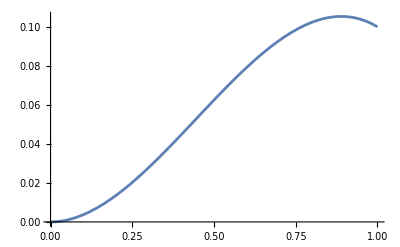

```mathematica
plotzexact=Plot[Evaluate[z[y]/.sol],{y,0,h},PlotRange->All]
```

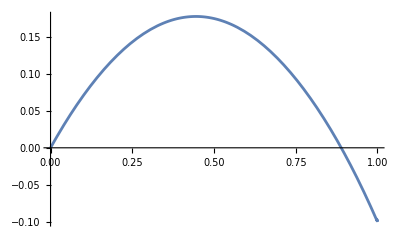

```mathematica
plotωexact=Plot[Evaluate[z'[y]/.sol],{y,0,h},PlotRange->All]
```

```mathematica
(*fit of the solution with a polynomial*)
```

```mathematica
tabz=Table[{y,Evaluate[z[y]/.sol][[1]]},{y,0,h,h/10}]
tabω=Table[{y,Evaluate[z'[y]/.sol][[1]]},{y,0,h,h/10}]
```

{{0,3.8002×10^-6},{1/10,0.00193092219},{1/5,0.00727488554},{3/10,0.0154030242},{2/5,0.0257048669},{1/2,0.037582486},{3/5,0.0504449759},{7/10,0.0637048804},{4/5,0.0767757862},{9/10,0.0890743559},{1,0.1}}

{{0,-5.775×10^-6},{1/10,0.037437771},{1/5,0.068392528},{3/10,0.093153929},{2/5,0.1118869},{1/2,0.12468182},{3/5,0.13158942},{7/10,0.1326314},{4/5,0.1278096},{9/10,0.117014},{1,0.100503782}}

```mathematica
NN=3;
```

```mathematica
fz[y_]:=Sum[c[i]y^i,{i,0,NN}]
fω[y_]:=Sum[d[i]y^i,{i,0,NN}]
```

```mathematica
fitz=FindFit[tabz,fz[y],Table[c[i],{i,0,NN}],y]
fitω=FindFit[tabω,fω[y],Table[d[i],{i,0,NN}],y]
```

{c[0]→-0.0000144541,c[1]→0.000862993,c[2]→0.198073,c[3]→-0.0989314}

{d[0]→0.000117,d[1]→0.4028,d[2]→-0.3114,d[3]→0.009095}

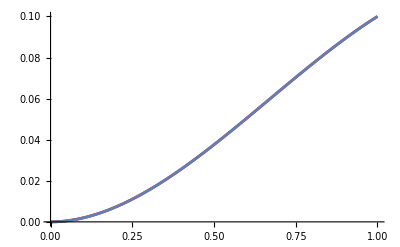

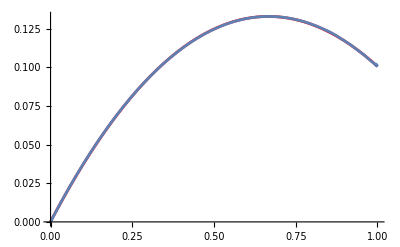

```mathematica
Show[Plot[fz[y]/.fitz,{y, 0,h},PlotStyle->Red],plotzexact]
Show[Plot[fω[y]/.fitω,{y, 0,h},PlotStyle->Red],plotωexact]
```

```mathematica
fz[y]/.fitz
fω[y]/.fitω
```

-0.0000144541+0.000862993 y+0.198073 y^2-0.0989314 y^3

0.000117+0.4028 y-0.3114 y^2+0.009095 y^3

```mathematica
(*check for z*)
```

```mathematica
t=Import["~/Documents/finite_elements/solution/z.csv"];
For[i=2; znum={}, i<=Length[t],i++,
If[Abs[t[[i,2]]-L/2]<0.1,AppendTo[znum,{t[[i,3]],t[[i,1]]}],0]
]
```

```mathematica
znum
```

{{0,0},{1,0.1},{0.90834,0.10525},{0.45,0.054322},{0.55,0.071642},{0.5,0.063053},{0.6,0.0796},{0.35,0.036795},{0.65,0.086968},{0.24972,0.020856},{0.29995,0.028435},{0.20067,0.014053},{0.1498,0.0083938},{0.093614,0.0032428},{0.81454,0.10352},{0.70241,0.093539},{0.75,0.098674},{0.39999,0.045406},{0.91518,0.10501},{0.83394,0.10445},{0.065066,0.0017655}}

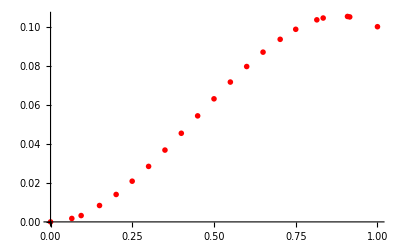

```mathematica
plotznum=ListPlot[znum,PlotStyle->{Red,PointSize->0.01}]
```

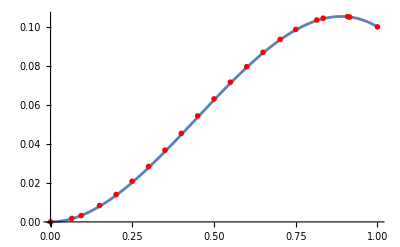

```mathematica
Show[plotzexact,plotznum]
```

```mathematica
(*check for ω*)
```

```mathematica
t=Import["~/Documents/finite_elements/solution/omega.csv"];
For[i=2; ωnum={}, i<=Length[t],i++,
If[Abs[t[[i,4]]-L/2]<0.1,AppendTo[ωnum,{t[[i,5]],t[[i,2]]}],0]
]
```

```mathematica
ωnum
```

{{0,-1.1546×10^-6},{1,-0.10051},{0.90834,-0.020713},{0.45,0.17725},{0.55,0.16618},{0.5,0.17397},{0.6,0.15374},{0.35,0.17019},{0.65,0.13775},{0.24972,0.14477},{0.29995,0.16024},{0.20067,0.12469},{0.1498,0.1057},{0.093614,0.068792},{0.81454,0.054321},{0.70241,0.11389},{0.75,0.096959},{0.39999,0.17596},{0.91518,-0.021144},{0.83394,0.041},{0.065066,0.049818}}

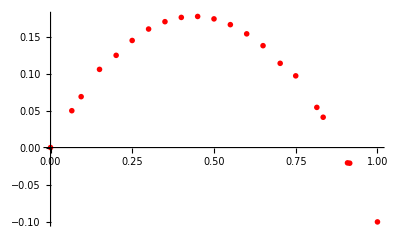

```mathematica
plotωnum=ListPlot[ωnum,PlotStyle->{Red,PointSize->0.01}]
```

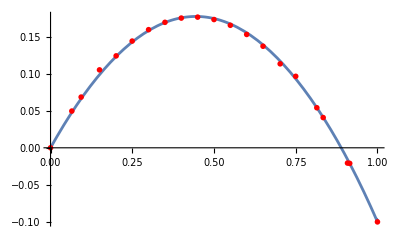

```mathematica
Show[plotωexact,plotωnum]
```